```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\tonnam_backup\Research_scratch\EG_Ag_MB3\Ag100_allsides\pmf_curve\layer\equilibrate\1_NPT

```mathematica
log=OpenRead["thermo.lammps"];
Find[log,"# Step PotEng"];
thermo=ReadList[log,{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
Sow[thermo];
```

```mathematica
Length[thermo]
```

5413

```mathematica
TimeSkip=1000;
```

```mathematica
Tavg=Mean[thermo[[All,5]]]
```

299.993

```mathematica
Tstd=StandardDeviation[thermo[[All,5]]]
```

3.49969

```mathematica
Tavg2=Mean[thermo[[TimeSkip;;Length[thermo],5]]]
```

299.979

```mathematica
Tstd2=StandardDeviation[thermo[[TimeSkip;;Length[thermo],5]]]
```

3.49545

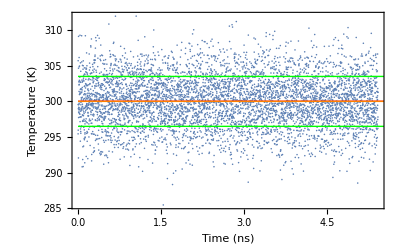

```mathematica
TGraph=Show[ListPlot[Partition[Riffle[thermo[[All,1]]/1000000,thermo[[All,5]]],2]],Plot[{Tavg,Tavg2},{x,0,100},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Tavg2+Tstd2,Tavg2-Tstd2},{x,0,100},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (ns)","Temperature (K)"}]
```

```mathematica
Pavg=Mean[thermo[[All,7]]]
```

-4.56867

```mathematica
Pstd=StandardDeviation[thermo[[All,7]]]
```

862.665

```mathematica
Pavg2=Mean[thermo[[TimeSkip;;Length[thermo],7]]]
```

-9.24157

```mathematica
Pstd2=StandardDeviation[thermo[[TimeSkip;;Length[thermo],7]]]
```

861.465

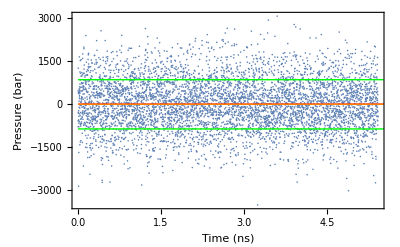

```mathematica
PGraph=Show[ListPlot[Partition[Riffle[thermo[[All,1]]/1000000,thermo[[All,7]]],2]],Plot[{Pavg,Pavg2},{x,0,100},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Pavg2+Pstd2,Pavg2-Pstd2},{x,0,100},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (ns)","Pressure (bar)"}]
```

```mathematica
Volavg=Mean[thermo[[All,6]]]
```

50766.6

```mathematica
Volstd=StandardDeviation[thermo[[All,6]]]
```

274.975

```mathematica
Volavg2=Mean[thermo[[TimeSkip;;Length[thermo],6]]]
```

50757.3

```mathematica
Volstd2=StandardDeviation[thermo[[TimeSkip;;Length[thermo],6]]]
```

261.386

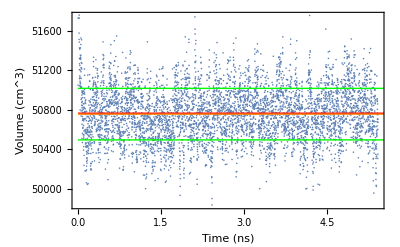

```mathematica
VGraph=Show[ListPlot[Partition[Riffle[thermo[[All,1]]/1000000,thermo[[All,6]]],2]],Plot[{Volavg,Volavg2},{x,0,100},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Volavg2+Volstd2,Volavg2-Volstd2},{x,0,100},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (ns)","Volume (cm^3)"}]
```

```mathematica
Engavg=Mean[thermo[[All,2]]]
```

-2184.28

```mathematica
Engstd=StandardDeviation[thermo[[All,2]]]
```

3.04043

```mathematica
Engavg2=Mean[thermo[[TimeSkip;;Length[thermo],2]]]
```

-2184.37

```mathematica
Engstd2=StandardDeviation[thermo[[TimeSkip;;Length[thermo],2]]]
```

2.72307

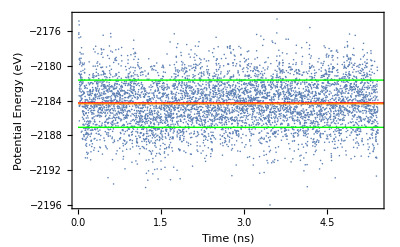

```mathematica
EGraph=Show[ListPlot[Partition[Riffle[thermo[[All,1]]/1000000,thermo[[All,2]]],2]],Plot[{Engavg,Engavg2},{x,0,100},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Engavg2+Engstd2,Engavg2-Engstd2},{x,0,100},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (ns)","Potential Energy (eV)"}]
```

```mathematica
CreateDirectory["graph"];
```

```mathematica
Export["graph/Tgraph.png",TGraph,ImageResolution->300];
Export["graph/Pgraph.png",PGraph,ImageResolution->300];
Export["graph/Vgraph.png",VGraph,ImageResolution->300];
Export["graph/Egraph.png",EGraph,ImageResolution->300];
```

```mathematica
Export["graph/report.txt",{"Tavg:",Tavg," ","Tstd:",Tstd," ","Pavg:",Pavg2," ","Pstd:",Pstd2," ","Volavg:",Volavg2," ","Volstd:",Volstd2," ","PotEngavg:",Engavg2," ","PotEngstd:",Engstd2}]
```

graph/report.txt